{{1,2,2.224566 MeV},{6,12,92.16173 MeV},{12,24,198.257 MeV},{24,53,464.2882 MeV},{29,63,551.3844 MeV},{36,84,732.2571 MeV},{42,98,846.2423 MeV},{74,184,1472.936 MeV},{80,200,1581.18 MeV},{92,238,1801.69 MeV}}

{{2,1.112283 MeV},{12,7.680144 MeV},{24,8.260709 MeV},{53,8.760155 MeV},{63,8.752134 MeV},{84,8.717347 MeV},{98,8.635125 MeV},{184,8.005087 MeV},{200,7.905899 MeV},{238,7.57012 MeV}}

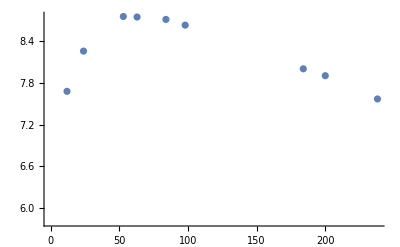

```mathematica
data=List[{1,2,2 IsotopeData[{1,2},"BindingEnergy"]},
{6,12,12 IsotopeData[{6,12},"BindingEnergy"]},
{12,24,24 IsotopeData[{12,24},"BindingEnergy"]},
{24,53,53 IsotopeData[{24,53},"BindingEnergy"]},
{29,63,63 IsotopeData[{29,63},"BindingEnergy"]},
{36,84,84 IsotopeData[{36,84},"BindingEnergy"]},
{42,98,98 IsotopeData[{42,98},"BindingEnergy"]},
{74,184,184 IsotopeData[{74,184},"BindingEnergy"]},
{80,200,200 IsotopeData[{80,200},"BindingEnergy"]},
{92,238,238 IsotopeData[{92,238},"BindingEnergy"]}]

b=List[{2, IsotopeData[{1,2},"BindingEnergy"]},
{12,IsotopeData[{6,12},"BindingEnergy"]},
{24,IsotopeData[{12,24},"BindingEnergy"]},
{53,IsotopeData[{24,53},"BindingEnergy"]},
{63,IsotopeData[{29,63},"BindingEnergy"]},
{84,IsotopeData[{36,84},"BindingEnergy"]},
{98,IsotopeData[{42,98},"BindingEnergy"]},
{184,IsotopeData[{74,184},"BindingEnergy"]},
{200,IsotopeData[{80,200},"BindingEnergy"]},
{238,IsotopeData[{92,238},"BindingEnergy"]}]
ListPlot[b]
```

```mathematica
fitted=Fit[data,{a,a^(2/3),(z (z-1))/a^(1/3),(a-2 z)^2/a},{z,a}]
```

((a-2 z)^2 (-26.7504 MeV))/a+a^(2/3) (-15.7516 MeV)+((-1+z) z (-0.591989 MeV))/a^(1/3)+a (14.8559 MeV)

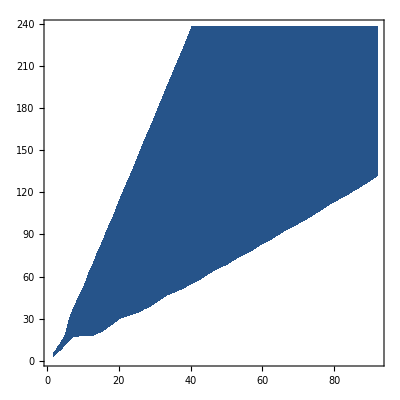

```mathematica
ContourPlot[fitted,{z,1,92},{a,1,238},PlotRange->{0,1}]
```